# Practical 7

## To plot the characteristics plot for a first order partial differential equation

## Question 1:

-2+3 y'[x]==0

{{y[x]→(2 x)/3+C[1]}}

{{1+(2 x)/3,-2+(2 x)/3,-1+(2 x)/3,3+(2 x)/3,4+(2 x)/3}}

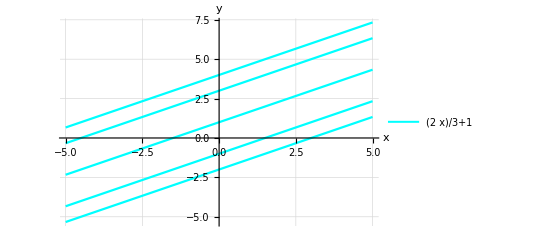

```mathematica
eqn1=3*y'[x]-2==0
sol1=DSolve[eqn1,y[x],x]
part1 = y[x]/.sol1/.C[1]->{1,-2,-1,3,4}
Plot[part1,{x,-5,5},AxesLabel->{x,y},PlotStyle->{Thickness[0.004],Cyan},PlotLegends->{part1},GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
```

## Question 2:

{{y[x]→C[1] Tan[x/2]}}

{{-10 Tan[x/2],0,10 Tan[x/2],20 Tan[x/2],30 Tan[x/2],40 Tan[x/2],50 Tan[x/2],60 Tan[x/2],70 Tan[x/2],80 Tan[x/2],90 Tan[x/2]}}

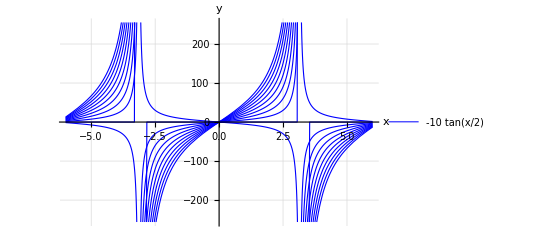

```mathematica
eqn2 := Sin[x]*y'[x]- y[x] == 0
sol2 = DSolve[eqn2, y[x],x]
part2 = y[x]/.sol2/.C[1]->{-10,0,10,20,30,40,50,60,70,80,90}
Plot[part2,{x,-6,6},AxesLabel->{x,y},PlotStyle->{Thickness[0.002],Blue},PlotLegends->{part2},GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
```

## Question 3:

{{y[x]→C[1] Sin[x]}}

{{-20 Sin[x],-10 Sin[x],0,10 Sin[x],20 Sin[x],30 Sin[x]}}

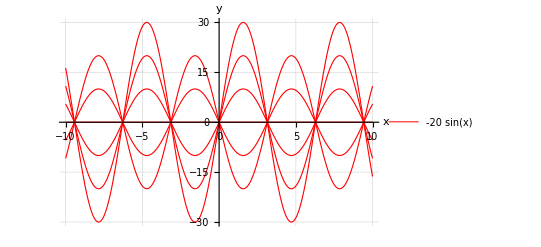

```mathematica
eqn2 := Sin[x]*y'[x]-Cos[x] y[x] == 0
sol2 = DSolve[eqn2, y[x],x]
part2 = y[x]/.sol2/.C[1]->{-20,-10,0,10,20,30}
Plot[part2,{x,-10,10},AxesLabel->{x,y},PlotStyle->{Thickness[0.002],Red},PlotLegends->{part2},GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
```

## Question 4:

{{y[x]→ⅇ^((2 ArcTanh[Tan[x/2]])/ⅇ) C[1]}}

{{10 ⅇ^((2 ArcTanh[Tan[x/2]])/ⅇ),20 ⅇ^((2 ArcTanh[Tan[x/2]])/ⅇ),30 ⅇ^((2 ArcTanh[Tan[x/2]])/ⅇ),40 ⅇ^((2 ArcTanh[Tan[x/2]])/ⅇ),50 ⅇ^((2 ArcTanh[Tan[x/2]])/ⅇ),60 ⅇ^((2 ArcTanh[Tan[x/2]])/ⅇ)}}

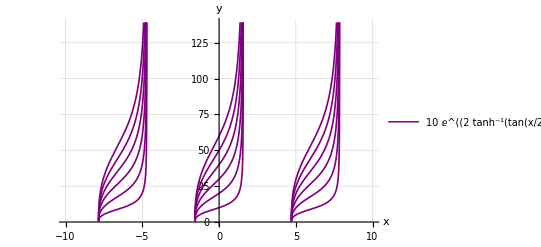

```mathematica
eqn2 := ⅇ*y'[x]-Sec[x] y[x] == 0
sol2 = DSolve[eqn2, y[x],x]
part2 = y[x]/.sol2/.C[1]->{10,20,30,40,50,60}
Plot[part2,{x,-10,10},AxesLabel->{x,y},PlotStyle->{Thickness[0.003],Purple},PlotLegends->{part2},GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
```

## Question 5:

{{y[x]→ⅇ^(-x^3/3) C[1]}}

{{-60 ⅇ^(-x^3/3),-50 ⅇ^(-x^3/3),-40 ⅇ^(-x^3/3),-30 ⅇ^(-x^3/3),-20 ⅇ^(-x^3/3),-10 ⅇ^(-x^3/3),0,10 ⅇ^(-x^3/3),20 ⅇ^(-x^3/3),30 ⅇ^(-x^3/3),40 ⅇ^(-x^3/3),50 ⅇ^(-x^3/3),60 ⅇ^(-x^3/3)}}

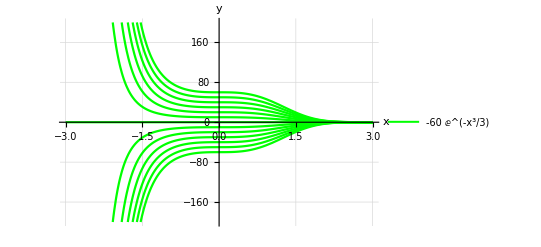

```mathematica
eqn2 := y'[x]+x^2* y[x] == 0
sol2 = DSolve[eqn2, y[x],x]
part2 = y[x]/.sol2/.C[1]->{-60,-50,-40,-30,-20,-10,0,10,20,30,40,50,60}
Plot[part2,{x,-3,3},AxesLabel->{x,y},PlotStyle->{Thickness[0.004],Green},PlotLegends->{part2},GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
```